# Catalan Numbers

Peter Burbery

Abstract

## Section

XXXX:

```mathematica
PacletInstall[ResourceObject["PeterBurbery/RecreationalMathematics"]]
```

PacletObject[…]

```mathematica
Needs["PeterBurbery`RecreationalMathematics`"]
```

Make a table of the Catalan numbers:

```mathematica
TableForm[Table[{n,CatalanNumber[n]},{n,16}]]
```

1 | 1
2 | 2
3 | 5
4 | 14
5 | 42
6 | 132
7 | 429
8 | 1430
9 | 4862
10 | 16796
11 | 58786
12 | 208012
13 | 742900
14 | 2674440
15 | 9694845
16 | 35357670

C_n=1/(n+1)(2n
n).

```mathematica
Table[1/(n+1)Binomial[2n,n],{n,16}]//Column
```

1
2
5
14
42
132
429
1430
4862
16796
58786
208012
742900
2674440
9694845
35357670

How many ways can 3 sets of parentheses be arranged? Answer:C_3.

```mathematica
CatalanNumber[3]
```

5

There are 5 ways:

```mathematica
AllBalancedGroupingSymbols[{"(",")"},3]
```

{((())),(()()),(())(),()(()),()()()}

```mathematica
Length[AllBalancedGroupingSymbols[{"(",")"},3]]
```

5

There are also Dyck paths:

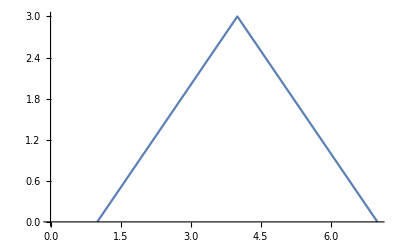
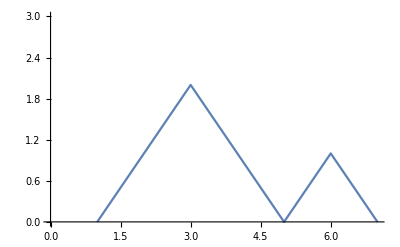
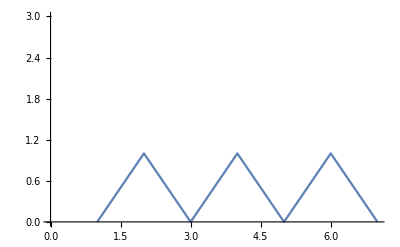
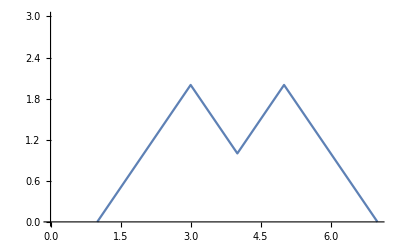
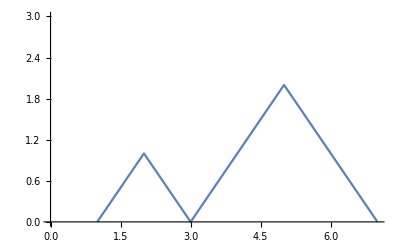
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
DyckPaths[3]//Multicolumn
```

How many n are there such that 1000≤n≤100,000 and C_n is odd?

```mathematica
Select[OddQ[CatalanNumber[#]]&][Range[1000,100000]]//AbsoluteTiming
```

{58.5496,{1023,2047,4095,8191,16383,32767,65535}}

```mathematica
Length[%60[[-1]]]
```

7

There are 7 numbers with odd Catalan numbers from 1000 to 100000.

What is the generating function for the Catalan numbers?

```mathematica
FindGeneratingFunction[CatalanNumber[Range[8]],n]//TraditionalForm
```

2/((√(1-4 n)+1) n)-1/n

```mathematica
Together[FindGeneratingFunction[CatalanNumber[Range[8]],n]]//TraditionalForm
```

(1-√(1-4 n))/((√(1-4 n)+1) n)

```mathematica
Simplify[FindGeneratingFunction[CatalanNumber[Range[8]],n]]//TraditionalForm
```

(2/(√(1-4 n)+1)-1)/n

```mathematica
Expand[FindGeneratingFunction[CatalanNumber[Range[8]],n]]
```

-1/n+2/((1+√(1-4 n)) n)

```mathematica
∑_(n=0)^∞ CatalanNumber[n] x^n
```

2/(1+√(1-4 x))

Restricted random walks with the Catalan numbers:

A man walks n blocks north and n blocks west of his residence. Every day he has 2n blocks to walk. How many routes are possible if he never crosses the diagonal line from home to office?

Visualize the walks:

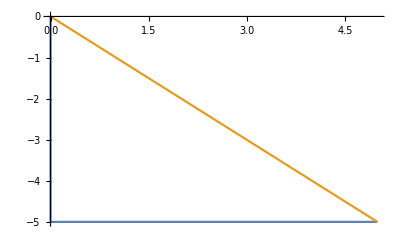
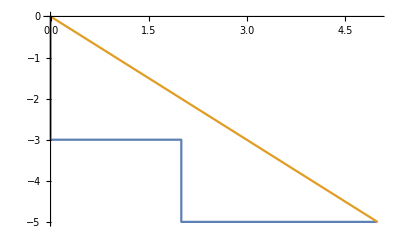
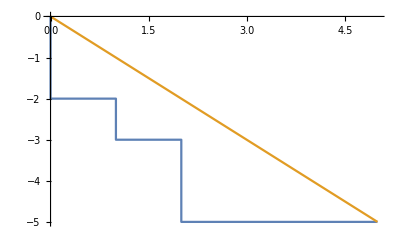
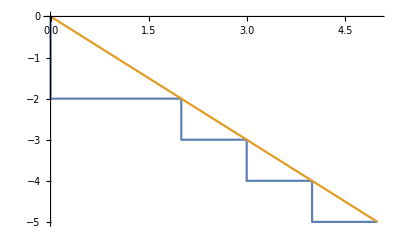
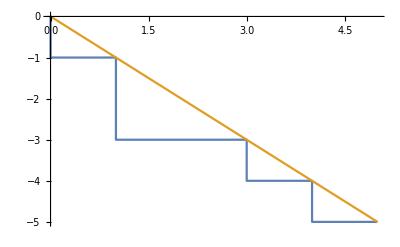
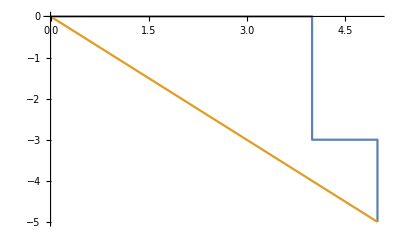
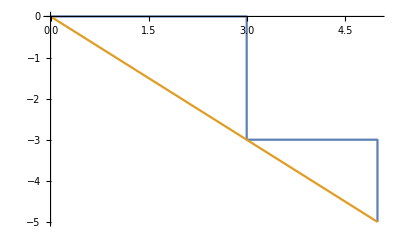
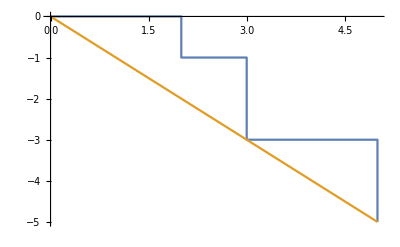
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
DiagonalWalkPlot[5,{1,-1}]//Multicolumn
```

```mathematica
Length[DiagonalWalkPlot[5,{1,-1}]]
```

84

There are 84 ways for the man to walk home.

### Asymptotics

```mathematica
Asymptotic[CatalanNumber[n],n->∞,SeriesTermGoal->2]
```

4^n/(n^(3/2) √π)

```mathematica
Asymptotic[CatalanNumber[n],n->∞,SeriesTermGoal->5]
```

4^n (-1155/(1024 n^(9/2) √π)+145/(128 n^(7/2) √π)-9/(8 n^(5/2) √π)+1/(n^(3/2) √π))

```mathematica
Asymptotic[CatalanNumber[n],n->∞,SeriesTermGoal->19]
```

4^n (-105666176941167049515/(73786976294838206464 n^(37/2) √π)+9898775194885242435/(9223372036854775808 n^(35/2) √π)-77871582933450075/(72057594037927936 n^(33/2) √π)+10265348737564125/(9007199254740992 n^(31/2) √π)-640669821436755/(562949953421312 n^(29/2) √π)+79183820728095/(70368744177664 n^(27/2) √π)-2475570313125/(2199023255552 n^(25/2) √π)+310496335695/(274877906944 n^(23/2) √π)-19402289907/(17179869184 n^(21/2) √π)+2421696563/(2147483648 n^(19/2) √π)-37844235/(33554432 n^(17/2) √π)+4735445/(4194304 n^(15/2) √π)-295911/(262144 n^(13/2) √π)+36939/(32768 n^(11/2) √π)-1155/(1024 n^(9/2) √π)+145/(128 n^(7/2) √π)-9/(8 n^(5/2) √π)+1/(n^(3/2) √π))

```mathematica
Simplify[%109]
```

1/(n^(37/2) √π)4^(-33+n) (-105666176941167049515+79190201559081939480 n-79740500923852876800 n^2+84093736858125312000 n^3-83973874835358351360 n^4+83030254003782942720 n^5-83066355732971520000 n^6+83348225458616401920 n^7-83332200618075881472 n^8+83208860311364829184 n^9-83220352853574942720 n^10+83306829443099525120 n^11-83291541833426927616 n^12+83179233317719375872 n^13-83226521113806766080 n^14+83586809083996405760 n^15-83010348331692982272 n^16+73786976294838206464 n^17)

### Recursion

Recursion formula for Catalan numbers:

```mathematica
RSolve[c[0]==1&&c[n+1]==(2(2n+1))/(n+2)c[n],c[n], n]
```

{{c[n]→(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n]}}

```mathematica
{{c[n]->(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n]}}⟦1,1,2⟧
```

(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n]

```mathematica
FullSimplify[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n]]
```

(4^n Gamma[1/2+n])/(√π Gamma[2+n])

```mathematica
FullSimplify[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n]-CatalanNumber[n]]
```

0

```mathematica
RSolve[c[0]==1&&c[n+1]==(2(2n+1))/(n+2)c[n],c[n], n][[1,1,2]]
```

(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n]

```mathematica
ZTransform[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n],n,z]
```

-1/2 (-1+√(1-4/z)) z

```mathematica
InverseZTransform[ZTransform[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n],n,z],z,n]
```

-(-1)^(1+n) 2^(1+2 n) Binomial[1/2,1+n]

```mathematica
GeneratingFunction[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n],n,x]
```

-(-1+√(1-4 x))/(2 x)

```mathematica
Table[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n],{n,1,20}]
```

{1,2,5,14,42,132,429,1430,4862,16796,58786,208012,742900,2674440,9694845,35357670,129644790,477638700,1767263190,6564120420}

```mathematica
FunctionExpand[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n]]
```

(4^n Gamma[1/2+n])/(√π Gamma[2+n])

```mathematica
FunctionRange[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n],{},n]
```

n-(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n]==0

```mathematica
FunctionDomain[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n],n]
```

(1/2+n∉ℤ&&Pochhammer[3,-1+n]≠0&&n>-2)||(Pochhammer[3,-1+n]≠0&&n>-1/2)||(n∉ℤ&&1/2+n∉ℤ&&Pochhammer[3,-1+n]≠0)

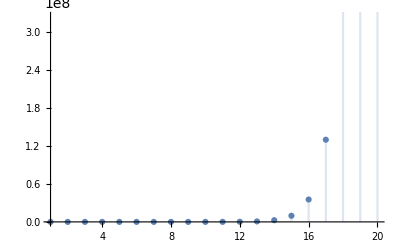

```mathematica
DiscretePlot[(4^(-1+n) Pochhammer[3/2,-1+n])/Pochhammer[3,-1+n],{n,1,20}]
```

```mathematica
CatalanNumber[7/2]
```

8192/(315 π)

```mathematica
CatalanNumber[n]//TraditionalForm
```

n

```mathematica
∑_(n=1)^∞ 1/CatalanNumber[n]
```

1/27 (27+4 √3 π)

```mathematica
∑_(n=1)^(m-1) 1/4^n CatalanNumber[n]
```

2^(-2 m) (2^(2 m)-2 Binomial[2 m,m])

```mathematica
CatalanNumber[CenteredInterval[7/2,3]]
```

```mathematica
ComplexPlot3D[CatalanNumber[n],{n,-2-2ⅈ,2+2ⅈ}]
```

-Graphics3D-

```mathematica
SetAttributes[f,{Flat,OneIdentity}]
```

```mathematica
e:CirclePlus[___,_List,___]:=Distribute[Unevaluated[e],List]
```

```mathematica
parenthesizedlist=f[a,b,c,d]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten
```

{a⊕(b⊕(c⊕d)),a⊕((b⊕c)⊕d),(a⊕b)⊕(c⊕d),(a⊕(b⊕c))⊕d,((a⊕b)⊕c)⊕d}

```mathematica
ParenthesizedExpressions[n_]:=Block[{f},SetAttributes[f,{Flat,OneIdentity}];
e:CirclePlus[___,_List,___]:=Distribute[Unevaluated[e],
List];
f[Sequence@@Array[Indexed[x,##]&,n]]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten]
```

```mathematica
ParenthesizedExpressions[3]
```

{x1⊕(x2⊕x3),(x1⊕x2)⊕x3}

```mathematica
ParenthesizedExpressions[4]
```

{x1⊕(x2⊕(x3⊕x4)),x1⊕((x2⊕x3)⊕x4),(x1⊕x2)⊕(x3⊕x4),(x1⊕(x2⊕x3))⊕x4,((x1⊕x2)⊕x3)⊕x4}

```mathematica
ParenthesizedExpressions[5]
```

{x1⊕(x2⊕(x3⊕(x4⊕x5))),x1⊕(x2⊕((x3⊕x4)⊕x5)),x1⊕((x2⊕x3)⊕(x4⊕x5)),x1⊕((x2⊕(x3⊕x4))⊕x5),x1⊕(((x2⊕x3)⊕x4)⊕x5),(x1⊕x2)⊕(x3⊕(x4⊕x5)),(x1⊕x2)⊕((x3⊕x4)⊕x5),(x1⊕(x2⊕x3))⊕(x4⊕x5),((x1⊕x2)⊕x3)⊕(x4⊕x5),(x1⊕(x2⊕(x3⊕x4)))⊕x5,(x1⊕((x2⊕x3)⊕x4))⊕x5,((x1⊕x2)⊕(x3⊕x4))⊕x5,((x1⊕(x2⊕x3))⊕x4)⊕x5,(((x1⊕x2)⊕x3)⊕x4)⊕x5}

```mathematica
ParenthesizedExpressions[6]
```

{x1⊕(x2⊕(x3⊕(x4⊕(x5⊕x6)))),x1⊕(x2⊕(x3⊕((x4⊕x5)⊕x6))),x1⊕(x2⊕((x3⊕x4)⊕(x5⊕x6))),x1⊕(x2⊕((x3⊕(x4⊕x5))⊕x6)),x1⊕(x2⊕(((x3⊕x4)⊕x5)⊕x6)),x1⊕((x2⊕x3)⊕(x4⊕(x5⊕x6))),x1⊕((x2⊕x3)⊕((x4⊕x5)⊕x6)),x1⊕((x2⊕(x3⊕x4))⊕(x5⊕x6)),x1⊕(((x2⊕x3)⊕x4)⊕(x5⊕x6)),x1⊕((x2⊕(x3⊕(x4⊕x5)))⊕x6),x1⊕((x2⊕((x3⊕x4)⊕x5))⊕x6),x1⊕(((x2⊕x3)⊕(x4⊕x5))⊕x6),x1⊕(((x2⊕(x3⊕x4))⊕x5)⊕x6),x1⊕((((x2⊕x3)⊕x4)⊕x5)⊕x6),(x1⊕x2)⊕(x3⊕(x4⊕(x5⊕x6))),(x1⊕x2)⊕(x3⊕((x4⊕x5)⊕x6)),(x1⊕x2)⊕((x3⊕x4)⊕(x5⊕x6)),(x1⊕x2)⊕((x3⊕(x4⊕x5))⊕x6),(x1⊕x2)⊕(((x3⊕x4)⊕x5)⊕x6),(x1⊕(x2⊕x3))⊕(x4⊕(x5⊕x6)),(x1⊕(x2⊕x3))⊕((x4⊕x5)⊕x6),((x1⊕x2)⊕x3)⊕(x4⊕(x5⊕x6)),((x1⊕x2)⊕x3)⊕((x4⊕x5)⊕x6),(x1⊕(x2⊕(x3⊕x4)))⊕(x5⊕x6),(x1⊕((x2⊕x3)⊕x4))⊕(x5⊕x6),((x1⊕x2)⊕(x3⊕x4))⊕(x5⊕x6),((x1⊕(x2⊕x3))⊕x4)⊕(x5⊕x6),(((x1⊕x2)⊕x3)⊕x4)⊕(x5⊕x6),(x1⊕(x2⊕(x3⊕(x4⊕x5))))⊕x6,(x1⊕(x2⊕((x3⊕x4)⊕x5)))⊕x6,(x1⊕((x2⊕x3)⊕(x4⊕x5)))⊕x6,(x1⊕((x2⊕(x3⊕x4))⊕x5))⊕x6,(x1⊕(((x2⊕x3)⊕x4)⊕x5))⊕x6,((x1⊕x2)⊕(x3⊕(x4⊕x5)))⊕x6,((x1⊕x2)⊕((x3⊕x4)⊕x5))⊕x6,((x1⊕(x2⊕x3))⊕(x4⊕x5))⊕x6,(((x1⊕x2)⊕x3)⊕(x4⊕x5))⊕x6,((x1⊕(x2⊕(x3⊕x4)))⊕x5)⊕x6,((x1⊕((x2⊕x3)⊕x4))⊕x5)⊕x6,(((x1⊕x2)⊕(x3⊕x4))⊕x5)⊕x6,(((x1⊕(x2⊕x3))⊕x4)⊕x5)⊕x6,((((x1⊕x2)⊕x3)⊕x4)⊕x5)⊕x6}

```mathematica
ParenthesizedExpressions[7]
```

{x1⊕(x2⊕(x3⊕(x4⊕(x5⊕(x6⊕x7))))),x1⊕(x2⊕(x3⊕(x4⊕((x5⊕x6)⊕x7)))),x1⊕(x2⊕(x3⊕((x4⊕x5)⊕(x6⊕x7)))),x1⊕(x2⊕(x3⊕((x4⊕(x5⊕x6))⊕x7))),x1⊕(x2⊕(x3⊕(((x4⊕x5)⊕x6)⊕x7))),x1⊕(x2⊕((x3⊕x4)⊕(x5⊕(x6⊕x7)))),x1⊕(x2⊕((x3⊕x4)⊕((x5⊕x6)⊕x7))),x1⊕(x2⊕((x3⊕(x4⊕x5))⊕(x6⊕x7))),x1⊕(x2⊕(((x3⊕x4)⊕x5)⊕(x6⊕x7))),x1⊕(x2⊕((x3⊕(x4⊕(x5⊕x6)))⊕x7)),x1⊕(x2⊕((x3⊕((x4⊕x5)⊕x6))⊕x7)),x1⊕(x2⊕(((x3⊕x4)⊕(x5⊕x6))⊕x7)),x1⊕(x2⊕(((x3⊕(x4⊕x5))⊕x6)⊕x7)),x1⊕(x2⊕((((x3⊕x4)⊕x5)⊕x6)⊕x7)),x1⊕((x2⊕x3)⊕(x4⊕(x5⊕(x6⊕x7)))),x1⊕((x2⊕x3)⊕(x4⊕((x5⊕x6)⊕x7))),x1⊕((x2⊕x3)⊕((x4⊕x5)⊕(x6⊕x7))),x1⊕((x2⊕x3)⊕((x4⊕(x5⊕x6))⊕x7)),x1⊕((x2⊕x3)⊕(((x4⊕x5)⊕x6)⊕x7)),x1⊕((x2⊕(x3⊕x4))⊕(x5⊕(x6⊕x7))),x1⊕((x2⊕(x3⊕x4))⊕((x5⊕x6)⊕x7)),x1⊕(((x2⊕x3)⊕x4)⊕(x5⊕(x6⊕x7))),x1⊕(((x2⊕x3)⊕x4)⊕((x5⊕x6)⊕x7)),x1⊕((x2⊕(x3⊕(x4⊕x5)))⊕(x6⊕x7)),x1⊕((x2⊕((x3⊕x4)⊕x5))⊕(x6⊕x7)),x1⊕(((x2⊕x3)⊕(x4⊕x5))⊕(x6⊕x7)),x1⊕(((x2⊕(x3⊕x4))⊕x5)⊕(x6⊕x7)),x1⊕((((x2⊕x3)⊕x4)⊕x5)⊕(x6⊕x7)),x1⊕((x2⊕(x3⊕(x4⊕(x5⊕x6))))⊕x7),x1⊕((x2⊕(x3⊕((x4⊕x5)⊕x6)))⊕x7),x1⊕((x2⊕((x3⊕x4)⊕(x5⊕x6)))⊕x7),x1⊕((x2⊕((x3⊕(x4⊕x5))⊕x6))⊕x7),x1⊕((x2⊕(((x3⊕x4)⊕x5)⊕x6))⊕x7),x1⊕(((x2⊕x3)⊕(x4⊕(x5⊕x6)))⊕x7),x1⊕(((x2⊕x3)⊕((x4⊕x5)⊕x6))⊕x7),x1⊕(((x2⊕(x3⊕x4))⊕(x5⊕x6))⊕x7),x1⊕((((x2⊕x3)⊕x4)⊕(x5⊕x6))⊕x7),x1⊕(((x2⊕(x3⊕(x4⊕x5)))⊕x6)⊕x7),x1⊕(((x2⊕((x3⊕x4)⊕x5))⊕x6)⊕x7),x1⊕((((x2⊕x3)⊕(x4⊕x5))⊕x6)⊕x7),x1⊕((((x2⊕(x3⊕x4))⊕x5)⊕x6)⊕x7),x1⊕(((((x2⊕x3)⊕x4)⊕x5)⊕x6)⊕x7),(x1⊕x2)⊕(x3⊕(x4⊕(x5⊕(x6⊕x7)))),(x1⊕x2)⊕(x3⊕(x4⊕((x5⊕x6)⊕x7))),(x1⊕x2)⊕(x3⊕((x4⊕x5)⊕(x6⊕x7))),(x1⊕x2)⊕(x3⊕((x4⊕(x5⊕x6))⊕x7)),(x1⊕x2)⊕(x3⊕(((x4⊕x5)⊕x6)⊕x7)),(x1⊕x2)⊕((x3⊕x4)⊕(x5⊕(x6⊕x7))),(x1⊕x2)⊕((x3⊕x4)⊕((x5⊕x6)⊕x7)),(x1⊕x2)⊕((x3⊕(x4⊕x5))⊕(x6⊕x7)),(x1⊕x2)⊕(((x3⊕x4)⊕x5)⊕(x6⊕x7)),(x1⊕x2)⊕((x3⊕(x4⊕(x5⊕x6)))⊕x7),(x1⊕x2)⊕((x3⊕((x4⊕x5)⊕x6))⊕x7),(x1⊕x2)⊕(((x3⊕x4)⊕(x5⊕x6))⊕x7),(x1⊕x2)⊕(((x3⊕(x4⊕x5))⊕x6)⊕x7),(x1⊕x2)⊕((((x3⊕x4)⊕x5)⊕x6)⊕x7),(x1⊕(x2⊕x3))⊕(x4⊕(x5⊕(x6⊕x7))),(x1⊕(x2⊕x3))⊕(x4⊕((x5⊕x6)⊕x7)),(x1⊕(x2⊕x3))⊕((x4⊕x5)⊕(x6⊕x7)),(x1⊕(x2⊕x3))⊕((x4⊕(x5⊕x6))⊕x7),(x1⊕(x2⊕x3))⊕(((x4⊕x5)⊕x6)⊕x7),((x1⊕x2)⊕x3)⊕(x4⊕(x5⊕(x6⊕x7))),((x1⊕x2)⊕x3)⊕(x4⊕((x5⊕x6)⊕x7)),((x1⊕x2)⊕x3)⊕((x4⊕x5)⊕(x6⊕x7)),((x1⊕x2)⊕x3)⊕((x4⊕(x5⊕x6))⊕x7),((x1⊕x2)⊕x3)⊕(((x4⊕x5)⊕x6)⊕x7),(x1⊕(x2⊕(x3⊕x4)))⊕(x5⊕(x6⊕x7)),(x1⊕((x2⊕x3)⊕x4))⊕(x5⊕(x6⊕x7)),(x1⊕(x2⊕(x3⊕x4)))⊕((x5⊕x6)⊕x7),(x1⊕((x2⊕x3)⊕x4))⊕((x5⊕x6)⊕x7),((x1⊕x2)⊕(x3⊕x4))⊕(x5⊕(x6⊕x7)),((x1⊕x2)⊕(x3⊕x4))⊕((x5⊕x6)⊕x7),((x1⊕(x2⊕x3))⊕x4)⊕(x5⊕(x6⊕x7)),(((x1⊕x2)⊕x3)⊕x4)⊕(x5⊕(x6⊕x7)),((x1⊕(x2⊕x3))⊕x4)⊕((x5⊕x6)⊕x7),(((x1⊕x2)⊕x3)⊕x4)⊕((x5⊕x6)⊕x7),(x1⊕(x2⊕(x3⊕(x4⊕x5))))⊕(x6⊕x7),(x1⊕(x2⊕((x3⊕x4)⊕x5)))⊕(x6⊕x7),(x1⊕((x2⊕x3)⊕(x4⊕x5)))⊕(x6⊕x7),(x1⊕((x2⊕(x3⊕x4))⊕x5))⊕(x6⊕x7),(x1⊕(((x2⊕x3)⊕x4)⊕x5))⊕(x6⊕x7),((x1⊕x2)⊕(x3⊕(x4⊕x5)))⊕(x6⊕x7),((x1⊕x2)⊕((x3⊕x4)⊕x5))⊕(x6⊕x7),((x1⊕(x2⊕x3))⊕(x4⊕x5))⊕(x6⊕x7),(((x1⊕x2)⊕x3)⊕(x4⊕x5))⊕(x6⊕x7),((x1⊕(x2⊕(x3⊕x4)))⊕x5)⊕(x6⊕x7),((x1⊕((x2⊕x3)⊕x4))⊕x5)⊕(x6⊕x7),(((x1⊕x2)⊕(x3⊕x4))⊕x5)⊕(x6⊕x7),(((x1⊕(x2⊕x3))⊕x4)⊕x5)⊕(x6⊕x7),((((x1⊕x2)⊕x3)⊕x4)⊕x5)⊕(x6⊕x7),(x1⊕(x2⊕(x3⊕(x4⊕(x5⊕x6)))))⊕x7,(x1⊕(x2⊕(x3⊕((x4⊕x5)⊕x6))))⊕x7,(x1⊕(x2⊕((x3⊕x4)⊕(x5⊕x6))))⊕x7,(x1⊕(x2⊕((x3⊕(x4⊕x5))⊕x6)))⊕x7,(x1⊕(x2⊕(((x3⊕x4)⊕x5)⊕x6)))⊕x7,(x1⊕((x2⊕x3)⊕(x4⊕(x5⊕x6))))⊕x7,(x1⊕((x2⊕x3)⊕((x4⊕x5)⊕x6)))⊕x7,(x1⊕((x2⊕(x3⊕x4))⊕(x5⊕x6)))⊕x7,(x1⊕(((x2⊕x3)⊕x4)⊕(x5⊕x6)))⊕x7,(x1⊕((x2⊕(x3⊕(x4⊕x5)))⊕x6))⊕x7,(x1⊕((x2⊕((x3⊕x4)⊕x5))⊕x6))⊕x7,(x1⊕(((x2⊕x3)⊕(x4⊕x5))⊕x6))⊕x7,(x1⊕(((x2⊕(x3⊕x4))⊕x5)⊕x6))⊕x7,(x1⊕((((x2⊕x3)⊕x4)⊕x5)⊕x6))⊕x7,((x1⊕x2)⊕(x3⊕(x4⊕(x5⊕x6))))⊕x7,((x1⊕x2)⊕(x3⊕((x4⊕x5)⊕x6)))⊕x7,((x1⊕x2)⊕((x3⊕x4)⊕(x5⊕x6)))⊕x7,((x1⊕x2)⊕((x3⊕(x4⊕x5))⊕x6))⊕x7,((x1⊕x2)⊕(((x3⊕x4)⊕x5)⊕x6))⊕x7,((x1⊕(x2⊕x3))⊕(x4⊕(x5⊕x6)))⊕x7,((x1⊕(x2⊕x3))⊕((x4⊕x5)⊕x6))⊕x7,(((x1⊕x2)⊕x3)⊕(x4⊕(x5⊕x6)))⊕x7,(((x1⊕x2)⊕x3)⊕((x4⊕x5)⊕x6))⊕x7,((x1⊕(x2⊕(x3⊕x4)))⊕(x5⊕x6))⊕x7,((x1⊕((x2⊕x3)⊕x4))⊕(x5⊕x6))⊕x7,(((x1⊕x2)⊕(x3⊕x4))⊕(x5⊕x6))⊕x7,(((x1⊕(x2⊕x3))⊕x4)⊕(x5⊕x6))⊕x7,((((x1⊕x2)⊕x3)⊕x4)⊕(x5⊕x6))⊕x7,((x1⊕(x2⊕(x3⊕(x4⊕x5))))⊕x6)⊕x7,((x1⊕(x2⊕((x3⊕x4)⊕x5)))⊕x6)⊕x7,((x1⊕((x2⊕x3)⊕(x4⊕x5)))⊕x6)⊕x7,((x1⊕((x2⊕(x3⊕x4))⊕x5))⊕x6)⊕x7,((x1⊕(((x2⊕x3)⊕x4)⊕x5))⊕x6)⊕x7,(((x1⊕x2)⊕(x3⊕(x4⊕x5)))⊕x6)⊕x7,(((x1⊕x2)⊕((x3⊕x4)⊕x5))⊕x6)⊕x7,(((x1⊕(x2⊕x3))⊕(x4⊕x5))⊕x6)⊕x7,((((x1⊕x2)⊕x3)⊕(x4⊕x5))⊕x6)⊕x7,(((x1⊕(x2⊕(x3⊕x4)))⊕x5)⊕x6)⊕x7,(((x1⊕((x2⊕x3)⊕x4))⊕x5)⊕x6)⊕x7,((((x1⊕x2)⊕(x3⊕x4))⊕x5)⊕x6)⊕x7,((((x1⊕(x2⊕x3))⊕x4)⊕x5)⊕x6)⊕x7,(((((x1⊕x2)⊕x3)⊕x4)⊕x5)⊕x6)⊕x7}

```mathematica
SymbolicIndexedArray[x,9]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9}

```mathematica
?SymbolicIndexedArray
```

```mathematica
f[x1,x2,x3,x4]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten
```

{x1⊕(x2⊕(x3⊕x4)),x1⊕((x2⊕x3)⊕x4),(x1⊕x2)⊕(x3⊕x4),(x1⊕(x2⊕x3))⊕x4,((x1⊕x2)⊕x3)⊕x4}

```mathematica
f[x1,x2,x3,x4,x5,x6]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten
```

{x1⊕(x2⊕(x3⊕(x4⊕(x5⊕x6)))),x1⊕(x2⊕(x3⊕((x4⊕x5)⊕x6))),x1⊕(x2⊕((x3⊕x4)⊕(x5⊕x6))),x1⊕(x2⊕((x3⊕(x4⊕x5))⊕x6)),x1⊕(x2⊕(((x3⊕x4)⊕x5)⊕x6)),x1⊕((x2⊕x3)⊕(x4⊕(x5⊕x6))),x1⊕((x2⊕x3)⊕((x4⊕x5)⊕x6)),x1⊕((x2⊕(x3⊕x4))⊕(x5⊕x6)),x1⊕(((x2⊕x3)⊕x4)⊕(x5⊕x6)),x1⊕((x2⊕(x3⊕(x4⊕x5)))⊕x6),x1⊕((x2⊕((x3⊕x4)⊕x5))⊕x6),x1⊕(((x2⊕x3)⊕(x4⊕x5))⊕x6),x1⊕(((x2⊕(x3⊕x4))⊕x5)⊕x6),x1⊕((((x2⊕x3)⊕x4)⊕x5)⊕x6),(x1⊕x2)⊕(x3⊕(x4⊕(x5⊕x6))),(x1⊕x2)⊕(x3⊕((x4⊕x5)⊕x6)),(x1⊕x2)⊕((x3⊕x4)⊕(x5⊕x6)),(x1⊕x2)⊕((x3⊕(x4⊕x5))⊕x6),(x1⊕x2)⊕(((x3⊕x4)⊕x5)⊕x6),(x1⊕(x2⊕x3))⊕(x4⊕(x5⊕x6)),(x1⊕(x2⊕x3))⊕((x4⊕x5)⊕x6),((x1⊕x2)⊕x3)⊕(x4⊕(x5⊕x6)),((x1⊕x2)⊕x3)⊕((x4⊕x5)⊕x6),(x1⊕(x2⊕(x3⊕x4)))⊕(x5⊕x6),(x1⊕((x2⊕x3)⊕x4))⊕(x5⊕x6),((x1⊕x2)⊕(x3⊕x4))⊕(x5⊕x6),((x1⊕(x2⊕x3))⊕x4)⊕(x5⊕x6),(((x1⊕x2)⊕x3)⊕x4)⊕(x5⊕x6),(x1⊕(x2⊕(x3⊕(x4⊕x5))))⊕x6,(x1⊕(x2⊕((x3⊕x4)⊕x5)))⊕x6,(x1⊕((x2⊕x3)⊕(x4⊕x5)))⊕x6,(x1⊕((x2⊕(x3⊕x4))⊕x5))⊕x6,(x1⊕(((x2⊕x3)⊕x4)⊕x5))⊕x6,((x1⊕x2)⊕(x3⊕(x4⊕x5)))⊕x6,((x1⊕x2)⊕((x3⊕x4)⊕x5))⊕x6,((x1⊕(x2⊕x3))⊕(x4⊕x5))⊕x6,(((x1⊕x2)⊕x3)⊕(x4⊕x5))⊕x6,((x1⊕(x2⊕(x3⊕x4)))⊕x5)⊕x6,((x1⊕((x2⊕x3)⊕x4))⊕x5)⊕x6,(((x1⊕x2)⊕(x3⊕x4))⊕x5)⊕x6,(((x1⊕(x2⊕x3))⊕x4)⊕x5)⊕x6,((((x1⊕x2)⊕x3)⊕x4)⊕x5)⊕x6}

```mathematica
ParenthesizedExpressions[n_,indexedsymbol_]:=Block[{f},SetAttributes[f,{Flat,OneIdentity}];
e:CirclePlus[___,_List,___]:=Distribute[Unevaluated[e],
List];
f[Sequence@@Array[Indexed[indexedsymbol,##]&,n]]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten]
```

```mathematica
NotebookDirectory[]
```

C:\Users\peter\Documents\GitHub\computational-essays\

```mathematica
ParenthesizedExpressions[5,e]
```

{e1⊕(e2⊕(e3⊕(e4⊕e5))),e1⊕(e2⊕((e3⊕e4)⊕e5)),e1⊕((e2⊕e3)⊕(e4⊕e5)),e1⊕((e2⊕(e3⊕e4))⊕e5),e1⊕(((e2⊕e3)⊕e4)⊕e5),(e1⊕e2)⊕(e3⊕(e4⊕e5)),(e1⊕e2)⊕((e3⊕e4)⊕e5),(e1⊕(e2⊕e3))⊕(e4⊕e5),((e1⊕e2)⊕e3)⊕(e4⊕e5),(e1⊕(e2⊕(e3⊕e4)))⊕e5,(e1⊕((e2⊕e3)⊕e4))⊕e5,((e1⊕e2)⊕(e3⊕e4))⊕e5,((e1⊕(e2⊕e3))⊕e4)⊕e5,(((e1⊕e2)⊕e3)⊕e4)⊕e5}

```mathematica
ParenthesizedExpressions[5,{b,c,d,e,f}]
```

{b⊕(c⊕(d⊕(e⊕f))),b⊕(c⊕((d⊕e)⊕f)),b⊕((c⊕d)⊕(e⊕f)),b⊕((c⊕(d⊕e))⊕f),b⊕(((c⊕d)⊕e)⊕f),(b⊕c)⊕(d⊕(e⊕f)),(b⊕c)⊕((d⊕e)⊕f),(b⊕(c⊕d))⊕(e⊕f),((b⊕c)⊕d)⊕(e⊕f),(b⊕(c⊕(d⊕e)))⊕f,(b⊕((c⊕d)⊕e))⊕f,((b⊕c)⊕(d⊕e))⊕f,((b⊕(c⊕d))⊕e)⊕f,(((b⊕c)⊕d)⊕e)⊕f}